```mathematica
Experiment3[g_,pre_,edge_]:=Block[{},
With[
{e=ChromaticPolynomial[EdgeDelete[g,edge],4],
t=ChromaticPolynomial[g,4]},
{e,t ,e-t}
]
]
```

```mathematica
Monitor[
Sort[
Tally[
Table[
With[
{g=ReadGrof[k]},
Experiment3[g,True,1<->2]]/24,{k,1,1000}]
]
],k]
```

{{{2,1,1},89},{{4,2,2},2},{{5,2,3},1},{{5,4,1},15},{{6,3,3},12},{{6,5,1},1},{{7,3,4},3},{{8,4,4},31},{{9,5,4},1},{{9,6,3},2},{{10,5,5},23},{{10,6,4},1},{{12,4,8},1},{{12,6,6},1},{{14,9,5},2},{{15,5,10},1},{{17,12,5},1},{{17,14,3},1},{{18,9,9},1},{{19,13,6},1},{{20,16,4},4},{{24,12,12},4},{{25,20,5},1},{{33,21,12},1}}

```mathematica
gef=Monitor[
Sort[
Tally[
Table[
With[
{g=ReadGrof[k]},
Experiment3[g,True,1<->2]]/24,{k,1,20000}]
]
],k]
```

{{{2,1,1},4620},{{3,1,2},176},{{4,2,2},286},{{4,3,1},2},{{5,1,4},4},{{5,2,3},9},{{5,4,1},694},{{6,2,4},1},{{6,3,3},1671},{{6,4,2},22},{{6,5,1},101},{{7,2,5},1},{{7,3,4},53},{{7,4,3},2},{{7,5,2},10},{{8,3,5},73},{{8,4,4},3099},{{8,5,3},16},{{8,6,2},19},{{9,3,6},24},{{9,4,5},3},{{9,5,4},155},{{9,6,3},89},{{9,7,2},1},{{10,4,6},6},{{10,5,5},2718},{{10,6,4},14},{{10,8,2},14},{{11,3,8},1},{{11,4,7},1},{{11,5,6},48},{{11,6,5},38},{{11,7,4},4},{{11,8,3},2},{{11,9,2},13},{{12,4,8},134},{{12,6,6},707},{{12,7,5},43},{{12,8,4},1},{{12,9,3},12},{{12,10,2},1},{{13,3,10},3},{{13,5,8},4},{{13,6,7},4},{{13,7,6},23},{{13,8,5},7},{{13,9,4},2},{{13,12,1},12},{{14,6,8},3},{{14,7,7},178},{{14,8,6},3},{{14,9,5},165},{{14,10,4},2},{{14,11,3},7},{{15,5,10},109},{{15,6,9},5},{{15,7,8},2},{{15,8,7},2},{{15,9,6},4},{{15,10,5},4},{{15,12,3},84},{{16,6,10},2},{{16,7,9},32},{{16,8,8},79},{{16,10,6},7},{{16,13,3},50},{{17,5,12},3},{{17,7,10},1},{{17,8,9},5},{{17,9,8},2},{{17,10,7},2},{{17,11,6},41},{{17,12,5},10},{{17,14,3},81},{{18,6,12},11},{{18,7,11},2},{{18,9,9},610},{{18,10,8},4},{{18,11,7},1},{{18,12,6},1},{{18,13,5},4},{{18,14,4},3},{{18,15,3},4},{{18,16,2},3},{{19,7,12},2},{{19,8,11},1},{{19,9,10},9},{{19,10,9},31},{{19,13,6},19},{{20,4,16},2},{{20,10,10},37},{{20,12,8},2},{{20,13,7},4},{{20,14,6},8},{{20,16,4},260},{{21,7,14},2},{{21,8,13},7},{{21,9,12},7},{{21,12,9},1},{{21,14,7},2},{{21,16,5},2},{{22,9,13},9},{{22,11,11},126},{{22,13,9},6},{{22,16,6},5},{{22,17,5},1},{{22,21,1},1},{{23,9,14},3},{{23,10,13},2},{{23,11,12},48},{{23,14,9},3},{{23,15,8},1},{{23,17,6},4},{{23,18,5},3},{{24,9,15},3},{{24,12,12},609},{{24,13,11},1},{{24,16,8},5},{{24,17,7},7},{{24,20,4},17},{{25,7,18},3},{{25,11,14},23},{{25,12,13},7},{{25,14,11},5},{{25,15,10},2},{{25,16,9},1},{{25,18,7},2},{{25,19,6},1},{{25,20,5},148},{{25,22,3},1},{{26,13,13},255},{{26,14,12},4},{{26,17,9},5},{{26,21,5},4},{{27,9,18},22},{{27,11,16},1},{{27,15,12},20},{{27,16,11},4},{{27,17,10},3},{{27,22,5},1},{{28,10,18},1},{{28,12,16},8},{{28,14,14},154},{{28,15,13},11},{{28,18,10},1},{{28,21,7},1},{{29,12,17},1},{{29,13,16},2},{{29,15,14},3},{{29,16,13},4},{{29,22,7},2},{{29,24,5},3},{{30,14,16},4},{{30,15,15},29},{{30,16,14},1},{{30,17,13},2},{{30,19,11},1},{{30,20,10},3},{{30,21,9},2},{{30,24,6},19},{{30,25,5},11},{{31,13,18},1},{{31,22,9},9},{{32,12,20},12},{{32,16,16},306},{{32,19,13},2},{{32,20,12},1},{{32,23,9},1},{{32,24,8},1},{{32,29,3},1},{{33,11,22},1},{{33,14,19},2},{{33,16,17},2},{{33,21,12},1},{{33,22,11},7},{{33,28,5},11},{{34,17,17},23},{{34,19,15},2},{{34,26,8},1},{{34,29,5},1},{{35,11,24},2},{{35,15,20},4},{{35,21,14},2},{{35,22,13},8},{{35,26,9},1},{{36,12,24},39},{{36,18,18},2},{{36,20,16},75},{{36,24,12},6},{{36,33,3},1},{{37,25,12},2},{{37,30,7},4},{{38,19,19},9},{{38,29,9},5},{{38,32,6},1},{{39,13,26},1},{{39,23,16},1},{{39,26,13},1},{{40,15,25},8},{{40,20,20},263},{{40,32,8},1},{{40,37,3},1},{{41,20,21},1},{{41,25,16},2},{{41,30,11},2},{{42,14,28},1},{{42,21,21},86},{{42,22,20},1},{{42,28,14},3},{{43,29,14},1},{{44,15,29},2},{{44,20,24},2},{{44,22,22},61},{{45,23,22},2},{{45,25,20},51},{{45,30,15},2},{{45,32,13},4},{{45,36,9},11},{{46,23,23},2},{{46,25,21},6},{{46,33,13},2},{{46,40,6},4},{{48,16,32},4},{{48,19,29},2},{{48,23,25},1},{{48,24,24},14},{{48,28,20},1},{{48,36,12},2},{{48,37,11},3},{{49,27,22},2},{{49,29,20},2},{{49,40,9},1},{{50,21,29},3},{{50,22,28},2},{{50,25,25},57},{{51,23,28},11},{{51,29,22},3},{{51,38,13},1},{{52,20,32},1},{{52,26,26},1},{{52,28,24},1},{{52,48,4},1},{{53,41,12},4},{{54,27,27},2},{{54,30,24},4},{{55,33,22},2},{{56,28,28},65},{{56,36,20},18},{{56,45,11},1},{{57,29,28},2},{{58,29,29},38},{{60,12,48},1},{{60,20,40},1},{{60,30,30},3},{{60,31,29},2},{{60,45,15},1},{{60,48,12},18},{{63,21,42},4},{{63,34,29},1},{{63,51,12},1},{{64,28,36},1},{{64,52,12},1},{{65,25,40},1},{{65,44,21},1},{{65,52,13},3},{{65,54,11},1},{{66,33,33},6},{{66,38,28},1},{{68,48,20},4},{{68,49,19},1},{{68,56,12},2},{{70,45,25},3},{{70,56,14},1},{{72,36,36},7},{{72,60,12},1},{{73,60,13},1},{{75,34,41},1},{{75,46,29},2},{{78,38,40},2},{{80,40,40},2},{{80,64,16},8},{{81,45,36},2},{{82,41,41},18},{{85,60,25},2},{{85,76,9},1},{{87,43,44},1},{{88,44,44},14},{{90,45,45},4},{{91,62,29},1},{{92,44,48},2},{{95,54,41},1},{{96,48,48},27},{{100,80,20},3},{{102,51,51},1},{{102,61,41},2},{{105,76,29},1},{{105,77,28},1},{{105,84,21},1},{{108,54,54},4},{{108,60,48},3},{{113,92,21},1},{{120,60,60},7},{{128,64,64},2},{{129,85,44},1},{{140,112,28},1},{{144,80,64},1},{{152,76,76},1},{{168,84,84},1},{{170,85,85},1},{{184,92,92},1},{{257,172,85},1}}

```mathematica
TableForm[gef,TableDepth->2]
```

{2,1,1} | 4620
{3,1,2} | 176
{4,2,2} | 286
{4,3,1} | 2
{5,1,4} | 4
{5,2,3} | 9
{5,4,1} | 694
{6,2,4} | 1
{6,3,3} | 1671
{6,4,2} | 22
{6,5,1} | 101
{7,2,5} | 1
{7,3,4} | 53
{7,4,3} | 2
{7,5,2} | 10
{8,3,5} | 73
{8,4,4} | 3099
{8,5,3} | 16
{8,6,2} | 19
{9,3,6} | 24
{9,4,5} | 3
{9,5,4} | 155
{9,6,3} | 89
{9,7,2} | 1
{10,4,6} | 6
{10,5,5} | 2718
{10,6,4} | 14
{10,8,2} | 14
{11,3,8} | 1
{11,4,7} | 1
{11,5,6} | 48
{11,6,5} | 38
{11,7,4} | 4
{11,8,3} | 2
{11,9,2} | 13
{12,4,8} | 134
{12,6,6} | 707
{12,7,5} | 43
{12,8,4} | 1
{12,9,3} | 12
{12,10,2} | 1
{13,3,10} | 3
{13,5,8} | 4
{13,6,7} | 4
{13,7,6} | 23
{13,8,5} | 7
{13,9,4} | 2
{13,12,1} | 12
{14,6,8} | 3
{14,7,7} | 178
{14,8,6} | 3
{14,9,5} | 165
{14,10,4} | 2
{14,11,3} | 7
{15,5,10} | 109
{15,6,9} | 5
{15,7,8} | 2
{15,8,7} | 2
{15,9,6} | 4
{15,10,5} | 4
{15,12,3} | 84
{16,6,10} | 2
{16,7,9} | 32
{16,8,8} | 79
{16,10,6} | 7
{16,13,3} | 50
{17,5,12} | 3
{17,7,10} | 1
{17,8,9} | 5
{17,9,8} | 2
{17,10,7} | 2
{17,11,6} | 41
{17,12,5} | 10
{17,14,3} | 81
{18,6,12} | 11
{18,7,11} | 2
{18,9,9} | 610
{18,10,8} | 4
{18,11,7} | 1
{18,12,6} | 1
{18,13,5} | 4
{18,14,4} | 3
{18,15,3} | 4
{18,16,2} | 3
{19,7,12} | 2
{19,8,11} | 1
{19,9,10} | 9
{19,10,9} | 31
{19,13,6} | 19
{20,4,16} | 2
{20,10,10} | 37
{20,12,8} | 2
{20,13,7} | 4
{20,14,6} | 8
{20,16,4} | 260
{21,7,14} | 2
{21,8,13} | 7
{21,9,12} | 7
{21,12,9} | 1
{21,14,7} | 2
{21,16,5} | 2
{22,9,13} | 9
{22,11,11} | 126
{22,13,9} | 6
{22,16,6} | 5
{22,17,5} | 1
{22,21,1} | 1
{23,9,14} | 3
{23,10,13} | 2
{23,11,12} | 48
{23,14,9} | 3
{23,15,8} | 1
{23,17,6} | 4
{23,18,5} | 3
{24,9,15} | 3
{24,12,12} | 609
{24,13,11} | 1
{24,16,8} | 5
{24,17,7} | 7
{24,20,4} | 17
{25,7,18} | 3
{25,11,14} | 23
{25,12,13} | 7
{25,14,11} | 5
{25,15,10} | 2
{25,16,9} | 1
{25,18,7} | 2
{25,19,6} | 1
{25,20,5} | 148
{25,22,3} | 1
{26,13,13} | 255
{26,14,12} | 4
{26,17,9} | 5
{26,21,5} | 4
{27,9,18} | 22
{27,11,16} | 1
{27,15,12} | 20
{27,16,11} | 4
{27,17,10} | 3
{27,22,5} | 1
{28,10,18} | 1
{28,12,16} | 8
{28,14,14} | 154
{28,15,13} | 11
{28,18,10} | 1
{28,21,7} | 1
{29,12,17} | 1
{29,13,16} | 2
{29,15,14} | 3
{29,16,13} | 4
{29,22,7} | 2
{29,24,5} | 3
{30,14,16} | 4
{30,15,15} | 29
{30,16,14} | 1
{30,17,13} | 2
{30,19,11} | 1
{30,20,10} | 3
{30,21,9} | 2
{30,24,6} | 19
{30,25,5} | 11
{31,13,18} | 1
{31,22,9} | 9
{32,12,20} | 12
{32,16,16} | 306
{32,19,13} | 2
{32,20,12} | 1
{32,23,9} | 1
{32,24,8} | 1
{32,29,3} | 1
{33,11,22} | 1
{33,14,19} | 2
{33,16,17} | 2
{33,21,12} | 1
{33,22,11} | 7
{33,28,5} | 11
{34,17,17} | 23
{34,19,15} | 2
{34,26,8} | 1
{34,29,5} | 1
{35,11,24} | 2
{35,15,20} | 4
{35,21,14} | 2
{35,22,13} | 8
{35,26,9} | 1
{36,12,24} | 39
{36,18,18} | 2
{36,20,16} | 75
{36,24,12} | 6
{36,33,3} | 1
{37,25,12} | 2
{37,30,7} | 4
{38,19,19} | 9
{38,29,9} | 5
{38,32,6} | 1
{39,13,26} | 1
{39,23,16} | 1
{39,26,13} | 1
{40,15,25} | 8
{40,20,20} | 263
{40,32,8} | 1
{40,37,3} | 1
{41,20,21} | 1
{41,25,16} | 2
{41,30,11} | 2
{42,14,28} | 1
{42,21,21} | 86
{42,22,20} | 1
{42,28,14} | 3
{43,29,14} | 1
{44,15,29} | 2
{44,20,24} | 2
{44,22,22} | 61
{45,23,22} | 2
{45,25,20} | 51
{45,30,15} | 2
{45,32,13} | 4
{45,36,9} | 11
{46,23,23} | 2
{46,25,21} | 6
{46,33,13} | 2
{46,40,6} | 4
{48,16,32} | 4
{48,19,29} | 2
{48,23,25} | 1
{48,24,24} | 14
{48,28,20} | 1
{48,36,12} | 2
{48,37,11} | 3
{49,27,22} | 2
{49,29,20} | 2
{49,40,9} | 1
{50,21,29} | 3
{50,22,28} | 2
{50,25,25} | 57
{51,23,28} | 11
{51,29,22} | 3
{51,38,13} | 1
{52,20,32} | 1
{52,26,26} | 1
{52,28,24} | 1
{52,48,4} | 1
{53,41,12} | 4
{54,27,27} | 2
{54,30,24} | 4
{55,33,22} | 2
{56,28,28} | 65
{56,36,20} | 18
{56,45,11} | 1
{57,29,28} | 2
{58,29,29} | 38
{60,12,48} | 1
{60,20,40} | 1
{60,30,30} | 3
{60,31,29} | 2
{60,45,15} | 1
{60,48,12} | 18
{63,21,42} | 4
{63,34,29} | 1
{63,51,12} | 1
{64,28,36} | 1
{64,52,12} | 1
{65,25,40} | 1
{65,44,21} | 1
{65,52,13} | 3
{65,54,11} | 1
{66,33,33} | 6
{66,38,28} | 1
{68,48,20} | 4
{68,49,19} | 1
{68,56,12} | 2
{70,45,25} | 3
{70,56,14} | 1
{72,36,36} | 7
{72,60,12} | 1
{73,60,13} | 1
{75,34,41} | 1
{75,46,29} | 2
{78,38,40} | 2
{80,40,40} | 2
{80,64,16} | 8
{81,45,36} | 2
{82,41,41} | 18
{85,60,25} | 2
{85,76,9} | 1
{87,43,44} | 1
{88,44,44} | 14
{90,45,45} | 4
{91,62,29} | 1
{92,44,48} | 2
{95,54,41} | 1
{96,48,48} | 27
{100,80,20} | 3
{102,51,51} | 1
{102,61,41} | 2
{105,76,29} | 1
{105,77,28} | 1
{105,84,21} | 1
{108,54,54} | 4
{108,60,48} | 3
{113,92,21} | 1
{120,60,60} | 7
{128,64,64} | 2
{129,85,44} | 1
{140,112,28} | 1
{144,80,64} | 1
{152,76,76} | 1
{168,84,84} | 1
{170,85,85} | 1
{184,92,92} | 1
{257,172,85} | 1

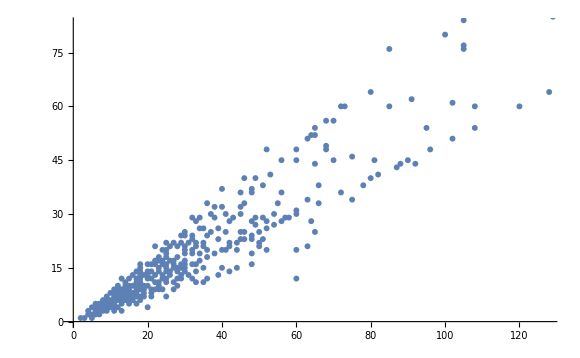

```mathematica
ListPlot[Map[Most[First[#]]&,gef]]
```

```mathematica
gef2=Monitor[
Sort[
Tally[
Table[
With[
{g=JacobsThalGraph2[k]},
Experiment3[g,True,1<->2]]/24,{k,2,12}]
]
],k]
```

{{{2/3,1/2,1/6},1},{{3/2,1,1/2},1},{{2,1,1},1},{{3,1,2},1},{{5,4,1},1},{{9,5,4},1},{{17,12,5},1},{{33,21,12},1},{{65,44,21},1},{{129,85,44},1},{{257,172,85},1}}

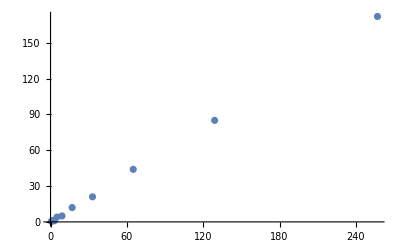

```mathematica
ListPlot[Map[Most[First[#]]&,gef2]]
```

```mathematica
Calc[k_]:=Calc[k]=With[
{g=Graph[plantri[[k]]]},
Experiment3[g,True,First[EdgeList[g]]]]
```

```mathematica
gef3=Monitor[
Table[
PrintTemporary[k];
Calc[k]/24,{k,1,600}]
,k]
```

{{18,10,8},{34,20,14},{46,32,14},{62,30,32},{59,27,32},{60,42,18},{48,16,32},{55,22,33},{58,32,26},{74,40,34},{77,44,33},{65,30,35},{87,48,39},{74,38,36},{94,52,42},{85,53,32},{69,34,35},{128,64,64},{124,78,46},{81,53,28},{108,48,60},{88,52,36},{152,84,68},{117,64,53},{91,48,43},{96,52,44},{151,80,71},{106,72,34},{143,65,78},{126,50,76},{144,82,62},{100,52,48},{84,36,48},{110,50,60},{127,69,58},{119,89,30},{108,60,48},{103,65,38},{118,60,58},{104,75,29},{136,104,32},{138,90,48},{152,80,72},{124,68,56},{106,64,42},{118,69,49},{194,96,98},{158,86,72},{158,86,72},{192,92,100},{161,97,64},{110,62,48},{179,128,51},{197,94,103},{175,87,88},{135,72,63},{166,96,70},{150,100,50},{176,106,70},{124,62,62},{122,71,51},{216,152,64},{140,72,68},{148,84,64},{136,82,54},{114,64,50},{167,102,65},{158,80,78},{142,62,80},{150,88,62},{140,72,68},{175,127,48},{160,82,78},{210,98,112},{117,54,63},{126,67,59},{168,89,79},{145,77,68},{157,74,83},{142,77,65},{123,68,55},{152,67,85},{128,72,56},{141,79,62},{134,68,66},{131,67,64},{139,76,63},{190,148,42},{101,72,29},{112,76,36},{116,57,59},{146,92,54},{178,98,80},{97,66,31},{125,72,53},{158,108,50},{162,72,90},{176,87,89},{164,96,68},{178,108,70},{164,112,52},{178,86,92},{156,94,62},{120,72,48},{241,148,93},{184,96,88},{224,116,108},{174,96,78},{136,84,52},{172,96,76},{162,112,50},{203,108,95},{176,96,80},{170,92,78},{164,92,72},{156,84,72},{164,106,58},{162,80,82},{158,88,70},{156,88,68},{226,111,115},{175,101,74},{195,123,72},{174,102,72},{188,94,94},{214,104,110},{145,67,78},{152,78,74},{174,100,74},{166,100,66},{137,81,56},{174,104,70},{274,160,114},{190,118,72},{238,124,114},{182,104,78},{264,128,136},{189,82,107},{202,108,94},{186,114,72},{248,126,122},{146,66,80},{151,72,79},{140,58,82},{194,98,96},{156,60,96},{176,89,87},{229,140,89},{180,106,74},{187,104,83},{197,108,89},{178,90,88},{161,74,87},{148,86,62},{220,136,84},{217,134,83},{179,86,93},{226,126,100},{191,104,87},{197,114,83},{176,110,66},{236,152,84},{199,107,92},{231,130,101},{187,84,103},{199,99,100},{157,86,71},{193,114,79},{158,91,67},{158,86,72},{163,75,88},{236,140,96},{163,90,73},{232,121,111},{194,106,88},{160,74,86},{195,98,97},{208,126,82},{286,184,102},{205,100,105},{240,124,116},{208,112,96},{218,103,115},{212,118,94},{245,97,148},{236,116,120},{220,114,106},{196,115,81},{246,150,96},{192,131,61},{173,86,87},{210,118,92},{172,97,75},{176,96,80},{176,112,64},{233,113,120},{200,98,102},{210,143,67},{198,92,106},{310,183,127},{252,148,104},{183,103,80},{178,88,90},{210,112,98},{181,94,87},{213,102,111},{171,90,81},{220,101,119},{215,127,88},{150,96,54},{170,109,61},{172,111,61},{183,95,88},{174,110,64},{186,110,76},{222,120,102},{138,64,74},{220,124,96},{252,125,127},{196,119,77},{228,124,104},{306,130,176},{244,95,149},{206,100,106},{154,81,73},{158,76,82},{214,110,104},{236,128,108},{186,90,96},{214,126,88},{226,109,117},{204,115,89},{274,140,134},{296,165,131},{271,129,142},{216,90,126},{205,104,101},{240,124,116},{250,146,104},{192,108,84},{167,88,79},{180,99,81},{191,114,77},{208,108,100},{146,64,82},{154,92,62},{177,103,74},{160,96,64},{226,140,86},{228,106,122},{224,138,86},{240,164,76},{160,86,74},{285,144,141},{164,72,92},{190,84,106},{174,84,90},{172,106,66},{178,106,72},{174,97,77},{187,100,87},{220,124,96},{281,165,116},{208,128,80},{218,116,102},{252,124,128},{266,120,146},{208,132,76},{180,108,72},{192,108,84},{168,96,72},{236,120,116},{186,112,74},{236,132,104},{180,100,80},{240,112,128},{215,115,100},{202,116,86},{169,104,65},{232,138,94},{145,101,44},{208,122,86},{295,120,175},{180,99,81},{214,124,90},{222,126,96},{254,134,120},{222,136,86},{261,145,116},{196,120,76},{168,110,58},{198,111,87},{181,136,45},{178,110,68},{270,154,116},{204,116,88},{218,132,86},{232,136,96},{276,180,96},{182,108,74},{264,124,140},{254,124,130},{310,132,178},{192,100,92},{280,132,148},{293,114,179},{195,130,65},{220,116,104},{324,144,180},{196,132,64},{253,136,117},{286,156,130},{220,136,84},{177,112,65},{222,99,123},{254,136,118},{239,151,88},{303,181,122},{233,103,130},{301,171,130},{244,114,130},{204,113,91},{214,104,110},{268,147,121},{196,122,74},{314,130,184},{234,114,120},{214,81,133},{274,148,126},{208,88,120},{244,138,106},{251,130,121},{237,150,87},{280,158,122},{211,138,73},{254,134,120},{236,124,112},{212,114,98},{251,134,117},{218,122,96},{310,220,90},{294,174,120},{241,127,114},{239,138,101},{250,148,102},{258,164,94},{208,138,70},{283,136,147},{344,125,219},{221,110,111},{193,89,104},{214,134,80},{251,130,121},{237,113,124},{276,166,110},{244,128,116},{236,120,116},{226,134,92},{236,134,102},{268,144,124},{230,114,116},{249,147,102},{213,106,107},{312,120,192},{306,154,152},{242,124,118},{264,148,116},{226,112,114},{182,98,84},{189,109,80},{220,106,114},{224,110,114},{200,126,74},{216,136,80},{208,104,104},{282,157,125},{244,178,66},{174,118,56},{270,167,103},{265,127,138},{258,138,120},{292,156,136},{247,131,116},{427,184,243},{375,174,201},{294,148,146},{256,153,103},{309,214,95},{245,150,95},{221,112,109},{268,122,146},{249,130,119},{207,122,85},{163,78,85},{252,148,104},{204,100,104},{238,116,122},{245,136,109},{243,161,82},{335,206,129},{254,108,146},{354,136,218},{204,80,124},{208,114,94},{253,142,111},{252,119,133},{286,140,146},{282,164,118},{280,140,140},{292,149,143},{202,118,84},{184,100,84},{194,106,88},{200,106,94},{253,106,147},{232,112,120},{180,88,92},{244,154,90},{209,133,76},{264,116,148},{250,134,116},{285,117,168},{319,155,164},{210,118,92},{290,156,134},{226,96,130},{276,174,102},{233,134,99},{234,132,102},{367,219,148},{302,194,108},{268,155,113},{208,118,90},{227,126,101},{281,178,103},{283,172,111},{226,138,88},{290,184,106},{178,108,70},{188,110,78},{276,154,122},{314,182,132},{236,156,80},{254,155,99},{221,111,110},{207,110,97},{212,115,97},{244,148,96},{313,222,91},{276,154,122},{276,156,120},{249,153,96},{289,143,146},{257,169,88},{224,132,92},{240,133,107},{230,125,105},{274,164,110},{297,164,133},{269,138,131},{233,124,109},{263,134,129},{178,96,82},{250,144,106},{316,208,108},{249,138,111},{235,109,126},{257,135,122},{202,80,122},{252,114,138},{332,240,92},{196,96,100},{190,80,110},{269,156,113},{221,114,107},{279,153,126},{258,123,135},{294,176,118},{216,114,102},{262,150,112},{264,148,116},{291,134,157},{364,175,189},{286,130,156},{326,124,202},{294,134,160},{278,128,150},{305,144,161},{256,110,146},{244,88,156},{321,154,167},{299,143,156},{263,126,137},{248,112,136},{170,87,83},{210,112,98},{222,118,104},{252,150,102},{182,78,104},{244,122,122},{270,124,146},{334,200,134},{276,154,122},{294,178,116},{303,186,117},{393,268,125},{232,116,116},{298,144,154},{282,150,132},{222,103,119},{298,180,118},{268,178,90},{236,112,124},{282,122,160},{262,132,130},{234,148,86},{227,103,124},{300,134,166},{324,166,158},{264,110,154},{209,107,102},{280,129,151},{322,138,184},{278,118,160},{252,139,113},{331,195,136},{432,256,176},{284,167,117},{290,174,116},{292,193,99},{274,173,101},{296,185,111},{249,150,99},{271,147,124},{281,136,145},{292,168,124},{292,173,119},{319,181,138},{277,156,121},{333,231,102},{307,177,130},{319,156,163},{266,159,107},{254,116,138},{241,134,107},{300,176,124},{369,211,158},{260,141,119},{284,155,129},{362,190,172},{276,136,140},{358,198,160},{300,176,124},{292,164,128},{272,150,122},{247,151,96},{280,160,120},{240,118,122},{248,112,136},{281,134,147},{240,138,102},{254,132,122},{219,96,123},{262,118,144},{220,122,98},{223,139,84},{283,168,115},{208,134,74},{216,135,81},{250,141,109},{295,153,142},{322,141,181},{233,124,109},{286,155,131},{294,162,132},{286,184,102},{247,166,81},{302,202,100},{244,132,112},{292,171,121},{299,178,121},{258,162,96},{263,182,81},{238,162,76},{218,98,120},{226,106,120},{248,128,120},{286,166,120},{264,144,120},{267,147,120},{320,200,120},{247,151,96},{212,116,96},{276,204,72},{194,120,74},{268,146,122},{217,113,104},{288,164,124},{256,139,117},{288,152,136}}

```mathematica
Map[First,%]
```

{{18,10,8},{34,20,14},{46,32,14},{48,16,32},{55,22,33},{58,32,26},{59,27,32},{60,42,18},{62,30,32},{74,40,34}}

```mathematica
Graph[plantri[[300]]]//VertexCount
```

21

```mathematica
ChromaticPolynomial[Graph[plantri[[300]]],x]//Timing
```

{37.8125,10002252792 x-59530452076 x^2+166819038132 x^3-294227949616 x^4+367900591625 x^5-347870422766 x^6+258811910123 x^7-155481647676 x^8+76727447824 x^9-31446351278 x^10+10770520829 x^11-3089511334 x^12+741007109 x^13-147780692 x^14+24259690 x^15-3226279 x^16+339261 x^17-27170 x^18+1558 x^19-57 x^20+x^21}

```mathematica
Map[#[[2]]/#[[3]]&,%]
```

{5/4,10/7,16/7,1/2,2/3,16/13,27/32,7/3,15/16,20/17}

```mathematica
Calc[k_]:=Calc[k]=With[
{g=Graph[plantri[[k]]]},
Experiment3[g,True,First[EdgeList[g]]]]/24
```

```mathematica
$HistoryLength=5
```

5

```mathematica
gef3=Monitor[
Table[Print[k];
Calc[k],{k,1,2000}]
,k]
```

```mathematica
$HistoryLength=3
```

3

```mathematica
Export["d:\\gef3.m",gef3]
```

d:\gef3.m

```mathematica
Sort[gef3]
```

$Aborted[]

```mathematica
{{18,10,8},{34,20,14},{46,32,14},{48,16,32},{55,22,33},{58,32,26},{59,27,32},{60,42,18},{62,30,32},{65,30,35},{69,34,35},{74,38,36},{74,40,34},{77,44,33},{81,53,28},{84,36,48},{85,53,32},{87,48,39},{88,52,36},{91,48,43},{94,52,42},{96,52,44},{97,66,31},{100,52,48},{101,72,29},{103,65,38},{104,75,29},{106,64,42},{106,72,34},{108,48,60},{108,60,48},{110,50,60},{110,62,48},{112,76,36},{114,64,50},{116,57,59},{117,54,63},{117,64,53},{118,60,58},{118,69,49},{119,89,30},{120,72,48},{122,71,51},{123,68,55},{124,62,62},{124,68,56},{124,78,46},{125,72,53},{126,50,76},{126,67,59},{127,69,58},{128,64,64},{128,72,56},{131,67,64},{134,68,66},{135,72,63},{136,82,54},{136,84,52},{136,104,32},{138,90,48},{139,76,63},{140,72,68},{140,72,68},{141,79,62},{142,62,80},{142,77,65},{143,65,78},{144,82,62},{145,67,78},{145,77,68},{146,92,54},{148,84,64},{150,88,62},{150,100,50},{151,80,71},{152,67,85},{152,78,74},{152,80,72},{152,84,68},{156,84,72},{156,88,68},{156,94,62},{157,74,83},{158,80,78},{158,86,72},{158,86,72},{158,88,70},{158,108,50},{160,82,78},{161,97,64},{162,72,90},{162,80,82},{162,112,50},{164,92,72},{164,96,68},{164,106,58},{164,112,52},{166,96,70},{166,100,66},{167,102,65},{168,89,79},{170,92,78},{172,96,76},{174,96,78},{174,100,74},{174,102,72},{175,87,88},{175,101,74},{175,127,48},{176,87,89},{176,96,80},{176,106,70},{178,86,92},{178,98,80},{178,108,70},{179,128,51},{184,96,88},{188,94,94},{190,148,42},{192,92,100},{194,96,98},{195,123,72},{197,94,103},{203,108,95},{210,98,112},{214,104,110},{216,152,64},{224,116,108},{226,111,115},{241,148,93}}
```

```mathematica
AllTrue[Map[With[
{rec=#},
rec[[3]]/4<=rec[[2]]<=rec[[3]]*4
]&,gef3],TrueQ]
```

True

```mathematica
AllTrue[Map[With[
{rec=#},
rec[[2]]/4<=rec[[3]]<=rec[[2]]*4
]&,gef3],TrueQ]
```

True

```mathematica
AllTrue[Map[With[
{rec=#},
rec[[2]]5/4<=rec[[1]]<=rec[[2]]*5
]&,gef3],TrueQ]
```

True

```mathematica
AllTrue[Map[With[
{rec=#},
rec[[3]]5/4<=rec[[1]]<=rec[[3]]*5
]&,gef3],TrueQ]
```

True

```mathematica
Length[gef3]
```

162

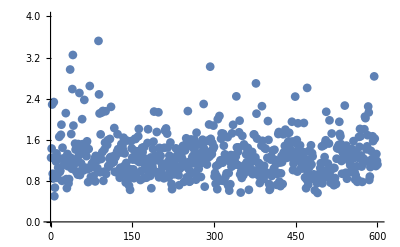

```mathematica
ListPlot[Map[#[[2]]/#[[3]]&,gef3], PlotRange->{All,{0,4}}, PlotMarkers->Automatic]
```

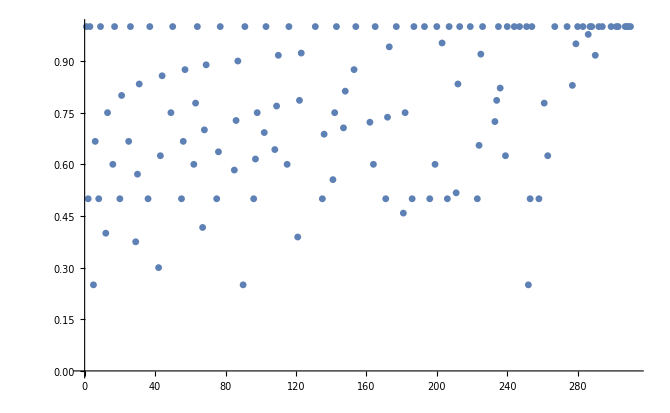

```mathematica
ListPlot[Map[First[#][[2]]/First[#][[3]]&,gef], PlotRange->{All,{0,1}}]
```

Part::partd: Part specification 18 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 18 ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification 34 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

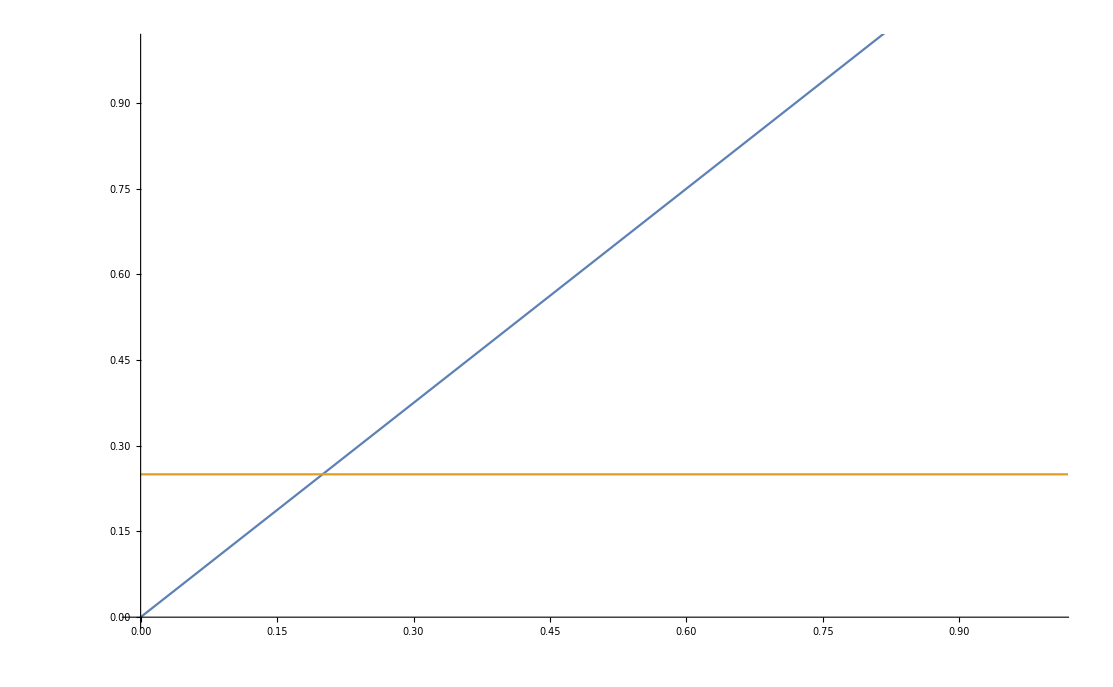

```mathematica
Show[
ListPlot[Map[First[#][[2]]/First[#][[3]]&,gef3], PlotRange->{All,{0,1}}],
Plot[{5x/4,0.25},{x,0,1000}]
]
```

```mathematica
Experiment5[g_,edge_]:=Block[{},
With[
{e=ChromaticPolynomial[EdgeDelete[g,edge],5],
t=ChromaticPolynomial[g,5]},
{e,t ,e-t}
]
]
```

```mathematica
Calc5[k_]:=Calc5[k]=With[
{g=Graph[plantri[[k]]]},
Experiment5[g,First[EdgeList[g]]]]/24
```

```mathematica
$HistoryLength=5
```

5

```mathematica
gef5=Monitor[
Table[PrintTemporary[k];
Calc5[k],{k,1,600}]
,k]
```

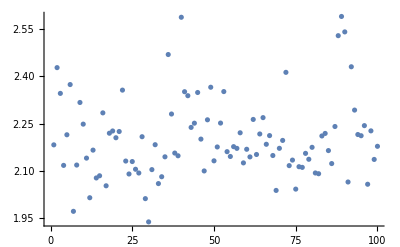

```mathematica
ListPlot[Map[#[[2]]/#[[3]]&,gef5], PlotRange->{All,All}]
```

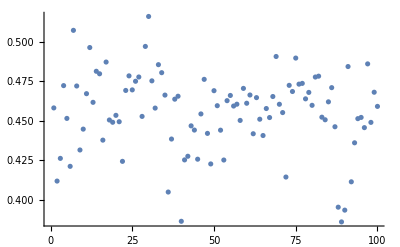

```mathematica
ListPlot[Map[#[[3]]/#[[2]]&,gef5], PlotRange->{All,All}]
```